```mathematica
(*Решение во временном пространстве*)
```

```mathematica
Clear[ic,i,iph1,iph,tau,t,r,c,x,k,t];
```

```mathematica
Clear[c,r];
```

```mathematica
iph[t_]=k*HeavisideLambda[t/tau-1];
```

```mathematica
tau=2×10^-9;k=1;
```

```mathematica
c=5×10^-12;r=1000;
```

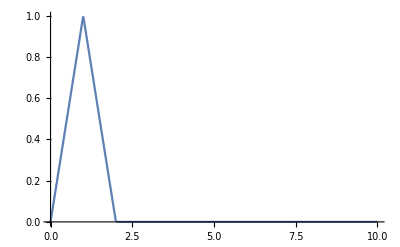

```mathematica
Plot[iph[t*tau], {t,0,10},PlotRange->Full]
```

```mathematica
sol=FullSimplify[DSolve[{(i[t]-iph[t])/c+i'[t]*r==0,i[0]==i[10*tau]},i[t],{t,0,10*tau}][[1]]];
```

```mathematica
f[t_]=i[t]/.sol
```

2 ⅇ^(-t/(c r)) ((250000000 c ⅇ^(1/(50000000 c r)) (-1+ⅇ^(1/(500000000 c r))) r)/(1+ⅇ^(1/(500000000 c r)) (1+ⅇ^(1/(500000000 c r))+ⅇ^(1/(250000000 c r))) (1+ⅇ^(3/(500000000 c r))+ⅇ^(3/(250000000 c r))))+(500000000 c ⅇ^(1/(500000000 c r)) r+ⅇ^(t/(c r)) (-1-500000000 c r+500000000 t)) HeavisideTheta[1/500000000-t]+(-250000000 c ⅇ^(1/(250000000 c r)) r+ⅇ^(t/(c r)) (1+250000000 c r-250000000 t)) HeavisideTheta[1/250000000-t])

```mathematica
Manipulate[Plot[%,{t,0,10*tau},PlotRange->All],{{c,5×10^-13},5×10^-13,1×10^-12},{{r,1000},100,5×10^3}](*,*)(*,{{k,0.001},0.001,5×10^3}]*)
```

```mathematica
(*Меандр со скважностью 2*)
```

```mathematica
c=5×10^-12;r=1000;
t0=FindRoot[f[t]==f[t+5*tau],{t,tau}];(*за t0 обозначим момент времени, когда компаратор должен изменить выходное напряжение, U0 - уровень компаратора*)
```

```mathematica
U0=(f[t]/.t0)*r
```

66.7173

```mathematica
(*Решение во частотном пространстве*)
```

```mathematica
(*2π/T=b, b из Фурье параметров*)
```

```mathematica
Clear[ic,i,iph1,iph,tau,t,r,c,x,k,t];
```

```mathematica
Clear[c,r];
```

```mathematica
tau=2×10^-9;k=1;b=-2*π/(10*tau);
```

```mathematica
cn[n_]=FourierCoefficient[iph[t],t,n,FourierParameters->{1, b}]
```

-(5 (-1+ⅇ^((ⅈ n π)/5))^2)/(2 n^2 π^2)

```mathematica
c0=Limit[cn[n],n->0];
```

```mathematica
solw1[t_]=FullSimplify[Sum[cn[n]*Exp[ⅈ*(-2*π/(10*tau))*n*t],{n,-Infinity,-1}]+Sum[cn[n]*Exp[ⅈ*(-2*π/(10*tau))*n*t],{n,1,Infinity}]+c0]
```

1/(10 π^2)(π^2-25 (PolyLog[2,ⅇ^(-100000000 ⅈ π t)]-2 PolyLog[2,(-1)^(1/5) ⅇ^(-100000000 ⅈ π t)]+PolyLog[2,(-1)^(2/5) ⅇ^(-100000000 ⅈ π t)])-25 (PolyLog[2,ⅇ^(100000000 ⅈ π t)]+PolyLog[2,-(-1)^(3/5) ⅇ^(100000000 ⅈ π t)]-2 PolyLog[2,-(-1)^(4/5) ⅇ^(100000000 ⅈ π t)]))

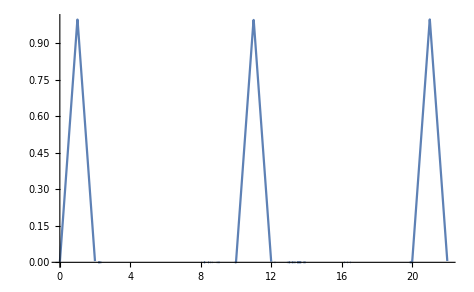

```mathematica
Plot[solw1[t*tau],{t,0,30},PlotRange->All]
```

```mathematica
cin[n_]=Solve[(i-cn[n])/(ⅈ*c*b*n)+i*r==0,i][[1]]
```

{i→(5 (-1+ⅇ^((ⅈ n π)/5))^2)/(2 n^2 π^2 (-1+100000000 ⅈ c n π r))}

```mathematica
cin0=Limit[i/.cin[n],n->0]
```

1/10

```mathematica
solw2[t_]=Simplify[Sum[(i/.cin[n])*Exp[ⅈ*(-2*π/(10*tau))*n*t],{n,-Infinity,-1}]+Sum[(i/.cin[n])*Exp[ⅈ*(-2*π/(10*tau))*n*t],{n,1,Infinity}]+cin0];
```

```mathematica
solw2[t];
```

```mathematica
Manipulate[Plot[%,{t,0,10*tau},PlotRange->All,WorkingPrecision->30],{{c,5×10^-13},5×10^-13,5×10^-12},{{r,1000},100,5×10^3}]
```

```mathematica
(*обратная задача*)
Clear[iph];
```

```mathematica
iph[t]=FullSimplify[f[t]+f'[t]*r*c]
```

2 ((-1+500000000 t) HeavisideTheta[1/500000000-t]+(1-250000000 t) HeavisideTheta[1/250000000-t])

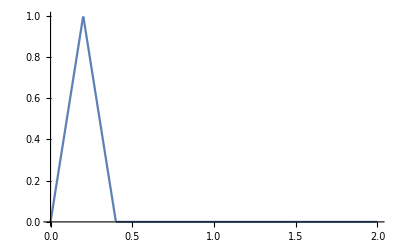

```mathematica
Plot[iph[t],{t,0,10*tau},PlotRange->All]
```